Degenerate internal squeezing -- threshold plots, poles of anti-squeezed quadrature versus minimum of squeezed quadrature definitions
NB: I am calling the points “singularities” for now to avoid confusion, but they are just the poles of the transfer functions (against complex Ω) at real χ such that they are on the real axis (and therefore real Ω).

```mathematica
(*want to find threshold (i.e. point of extremum for shot noise vs. χ) for loss detector, expect to reduce to χ=γR
--> it suffices to look at the poles of the anti-squeezed quadrature*)
$Assumptions={γbtot≥γR>0,ωs>0,Ω≥0,χ≥0,γa≥0,1>Rpd≥0};
Print[FullSimplify[(1-Rpd)(
ComplexExpand[Abs[(2γR-γbtot-χ+I Ω-ωs^2/(γa-I Ω))/(γbtot+χ-I Ω+ωs^2/(γa-I Ω))]^2]
+ComplexExpand[Abs[(2(γR (γbtot-γR))^(1/2))/(γbtot+χ-I Ω+ωs^2/(γa-I Ω))]^2]
+ComplexExpand[Abs[(2(γR γa)^(1/2)ωs)/((γbtot+χ-I Ω)(γa-I Ω)+ωs^2)]^2])+Rpd]]
Sx1[Ω_,χ_]:=((γa^2+Ω^2) (4 (-1+Rpd) γR χ+(γbtot+χ)^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4)/((γa^2+Ω^2) ((γbtot+χ)^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4)
Sx1[Ω,χ]==1-( 4 (1-Rpd) γR χ(γa^2+Ω^2) )/(Ω^4+Ω^2 (γa^2+(γbtot+χ)^2-2 ωs^2)+(γa (γbtot+χ)+ωs^2)^2)//Simplify
```

((γa^2+Ω^2) (γbtot^2+2 γbtot χ+4 (-1+Rpd) γR χ+χ^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4)/((γa^2+Ω^2) ((γbtot+χ)^2+Ω^2)+2 (γa (γbtot+χ)-Ω^2) ωs^2+ωs^4)

True

```mathematica
(*finding poles of anti-squeezed quadrature, requires χ->-χ at the start
- if instead looking for zeros of squeezed quadrature, these aren't robust to loss, so they will not always exist*)
sol=Solve[(Ω^4+Ω^2 (γa^2+(γbtot+χ)^2-2 ωs^2)+(γa (γbtot+χ)+ωs^2)^2==0)/.χ->-χ(*to enter anti-squeezed quadrature*),{Ω,χ}]//FullSimplify
(*reality condition on χ: Ω Abs[γa^2+Ω^2-ωs^2]*)
Solve[Ω Abs[γa^2+Ω^2-ωs^2]==0,Ω]
sol[[1;;2]]/.Ω->0//Simplify
sol[[1;;2]]/.Ω->(ωs^2-γa^2)^(1/2)//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{χ→(γbtot (γa^2+Ω^2)+γa ωs^2-ⅈ Ω Abs[γa^2+Ω^2-ωs^2])/(γa^2+Ω^2)},{χ→(γbtot (γa^2+Ω^2)+γa ωs^2+ⅈ Ω Abs[γa^2+Ω^2-ωs^2])/(γa^2+Ω^2)},{Ω→-ⅈ γa,χ→γa+γbtot+ωs^2/(2 γa)},{Ω→ⅈ γa,χ→γa+γbtot+ωs^2/(2 γa)}}

{{Ω→0},{Ω→-√(-γa^2+ωs^2)},{Ω→√(-γa^2+ωs^2)}}

{{χ→γbtot+ωs^2/γa},{χ→γbtot+ωs^2/γa}}

{{χ→γa+γbtot},{χ→γa+γbtot}}

```mathematica
(*zeros of squeezed quadrature*)
Solve[Sx1[Ω,χ]==0,{Ω,χ}]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{χ→-1/(γa^2+Ω^2)((γbtot+2 (-1+Rpd) γR) (γa^2+Ω^2)+γa ωs^2+√((4 (-1+Rpd) γR (γbtot+(-1+Rpd) γR)-Ω^2) (γa^2+Ω^2)^2+2 (γa^2+Ω^2) (2 (-1+Rpd) γa γR+Ω^2) ωs^2-Ω^2 ωs^4))},{χ→1/(γa^2+Ω^2)(-(γbtot+2 (-1+Rpd) γR) (γa^2+Ω^2)-γa ωs^2+√((4 (-1+Rpd) γR (γbtot+(-1+Rpd) γR)-Ω^2) (γa^2+Ω^2)^2+2 (γa^2+Ω^2) (2 (-1+Rpd) γa γR+Ω^2) ωs^2-Ω^2 ωs^4))}}

```mathematica
(*alternative method: find minimum of squeezed quadrature (which might NOT correspond to pole in anti-squeezed quadrature)
this works for degenerate internal squeezing but poles mess up analytics in non-degenerate case, hence why pole finding is a better general notion*)
DΩSx[Ω_,χ_]:=FullSimplify[D[Sx1[Ω0,χ0],Ω0]/.{Ω0->Ω,χ0->χ}]
DχSx[Ω_,χ_]:=FullSimplify[D[Sx1[Ω0,χ0],χ0]/.{Ω0->Ω,χ0->χ}]
GradSx[Ω_,χ_]:={DΩSx[Ω,χ],DχSx[Ω,χ]}
Sx1[ωs,γbtot]/.{γa->0,Rpd->0,γbtot->γR}//Simplify
DΩSx[ωs,γbtot]/.{γa->0}//Simplify
DχSx[ωs,γbtot]/.{γa->0}//Simplify

(*analytic solution for threshold*)
minSol=Solve[{GradSx[Ω,χ]=={0,0},Ω≥0,χ≥0,γbtot≥γR>0,ωs>0,γa≥0,1>Rpd≥0},{Ω,χ}]//Simplify;
Print["Solve[..., {Ω,χ}] found "<>ToString[Length[minSol]]<>" solutions"]
(*Root[f,k]represents the exactk^th root of the polynomial equationf[x]==0.*)

(*lossless limit*)
(minSol[[3]]/.{γa->0})//FullSimplify
Solve[(γbtot^3-4 γbtot ωs^2+(-γbtot^2+4 ωs^2) #1-γbtot #1^2+#1^3&)[χ]==0,χ]
Table[Solve[(ωs^4+(γbtot^2-2 ωs^2-(χ/.%[[j]][[1]])^2) #1^2+#1^4&)[Ω]==0,Ω],{j,1,Length[%]}]
(*problem: condition is false, first root is +ve*)
Solve[(-ωs^3-3 ωs^2 #1-2 ωs #1^2+2 #1^3&)[x]==0,x]
```

0

0

0

Solve[..., {Ω,χ}] found 6 solutions

Power::infy: Infinite expression 1/0 encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

{Ω→ConditionalExpression[Root[ωs^4+(γbtot^2-2 ωs^2-Root[γbtot^3-4 γbtot ωs^2+(-γbtot^2+4 ωs^2) #1-γbtot #1^2+#1^3&,2]^2) #1^2+#1^4&,2],Rpd>0&&γbtot>γR&&0<ComplexInfinity&&Root[-ωs^3-3 ωs^2 #1-2 ωs #1^2+2 #1^3&,1]<0&&(0>ComplexInfinity||2 ωs>γbtot)],χ→ConditionalExpression[Root[γbtot^3-4 γbtot ωs^2+(-γbtot^2+4 ωs^2) #1-γbtot #1^2+#1^3&,2],Rpd>0&&γbtot>γR&&0<ComplexInfinity&&Root[-ωs^3-3 ωs^2 #1-2 ωs #1^2+2 #1^3&,1]<0&&(0>ComplexInfinity||2 ωs>γbtot)]}

{{χ→γbtot},{χ→-√(γbtot^2-4 ωs^2)},{χ→√(γbtot^2-4 ωs^2)}}

{{{Ω→-ωs},{Ω→-ωs},{Ω→ωs},{Ω→ωs}},{{Ω→-ⅈ ωs},{Ω→-ⅈ ωs},{Ω→ⅈ ωs},{Ω→ⅈ ωs}},{{Ω→-ⅈ ωs},{Ω→-ⅈ ωs},{Ω→ⅈ ωs},{Ω→ⅈ ωs}}}

{{x→1/3 (ωs+(11 ωs^2)/(2^(1/3) (58 ωs^3+3 √78 ωs^3)^(1/3))+((58 ωs^3+3 √78 ωs^3)^(1/3))/2^(2/3))},{x→ωs/3-(11 (1+ⅈ √3) ωs^2)/(6 2^(1/3) (58 ωs^3+3 √78 ωs^3)^(1/3))-((1-ⅈ √3) (58 ωs^3+3 √78 ωs^3)^(1/3))/(6 2^(2/3))},{x→ωs/3-(11 (1-ⅈ √3) ωs^2)/(6 2^(1/3) (58 ωs^3+3 √78 ωs^3)^(1/3))-((1+ⅈ √3) (58 ωs^3+3 √78 ωs^3)^(1/3))/(6 2^(2/3))}}

```mathematica
(*plotting threshold points*)
(*parameters of LIGO Voyager from Li et al 2020*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);
Larm=4. 10^3(*m*);
Pcirc=3. 10^6(*W*);
λ0=2. 10^-6(*m*);
ω0=2π c/λ0;
γR=2π 500.(*Hz*);
ωs=10γR;
τRoundTripArm=(2 Larm)/c;
Tsrm=0.046;
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γR+-1/(2 τRoundTripSRC)Log[1-Tlb]
```

Power::infy: Infinite expression 1/0. encountered.

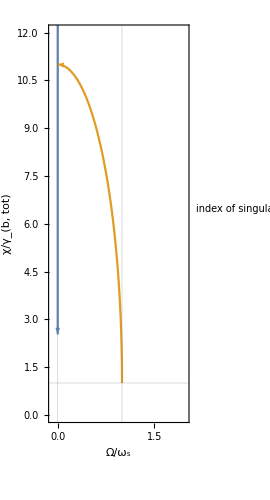

Power::infy: Infinite expression 1/0. encountered.

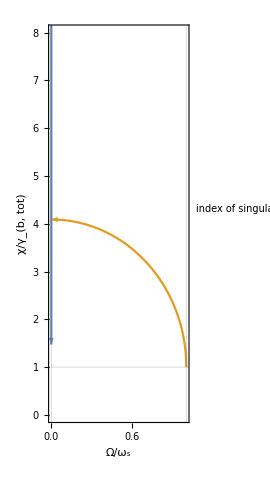

```mathematica
(*plotting pole-defined threshold values*)
poleSol={
{Ω->0,χ->γbtot+ωs^2/γa},
{Ω->(ωs^2-γa^2)^(1/2),χ->γa+γbtot}};
Clear[plotPoleThreshold]
plotPoleThreshold[Tlb0_,PlotRange0_:Automatic,PlotStyle0_:Automatic,isPlotLabelled_:True,isArrowed_:True]:=
Block[{
p1=ParametricPlot[
Evaluate[Table[{Ω/ωs,χ/γbtot}/.poleSol[[j]]/.{γa->γaFn[Tla],γbtot->γbtotFn[Tlb0]},{j,1,Length[poleSol]}]],
{Tla,0,1},Frame->True,FrameLabel->{{"χ/γ_(b, tot)",},{"Ω/ω_s",If[isPlotLabelled,StringForm["degenerate internal squeezing\nparameters of LIGO Voyager\nthreshold as singularities of anti-sqz'd quadrature\nas a function of T_(l, a)∈(0,1)\nT_(l, b)=``",Tlb0]]}},AspectRatio->Full,GridLines->{{0,1},{1}},PerformanceGoal->"Quality",PlotRange->PlotRange0,PlotStyle->PlotStyle0,PlotLegends->LineLegend[Range[Length[poleSol]],LabelStyle->Directive[10],LegendLabel->"index of singularity\nof antisqz.\nin solution set"]]},
If[isArrowed,p1/.Line[x__]:>Sequence[Arrowheads->{{0.05,0.999999}},Arrow[x]],p1]]

plotPoleThreshold[0,{{-0.1,2},{0,12}}]
(*changing Tlb doesn't affect slope, just χ axis scaling*)
plotPoleThreshold[0.1,{Automatic,{Automatic,8}}]
```

```mathematica
(*plotting threshold values from minima of squeezed quadrature method*)
Clear[plotSqzExtremePoints]
plotSqzExtremePoints[Tlb0_,Rpd0_,PlotRange0_:Automatic,PlotStyle0_:Dashed,isPlotLabelled_:True,isArrowed_:True]:=Block[{
p1=ParametricPlot[Evaluate[Table[({Ω/ωs,χ/γbtotFn[Tlb0]}/.minSol[[j]])/.{γa->γaFn[Tla],γbtot->γbtotFn[Tlb0],Rpd->Rpd0},
{j,1,Length[minSol]}]],
{Tla,0,1},Frame->True,FrameLabel->{{"χ/γ_(b, tot)",},{"Ω/ω_s",If[isPlotLabelled,StringForm["degenerate internal squeezing\nparameters of LIGO Voyager\nextrema of S_x(Ω,χ) (shot noise)\nas a function of T_(l, a)∈(0,1)\nT_(l, b)=``, R_PD=``",Tlb0,Rpd0]]}},AspectRatio->Full,GridLines->{{0,1},{1}},PlotLegends->LineLegend[Range[Length[minSol]],LabelStyle->Directive[10],LegendLabel->"index of extrema\nof sqz.\nin solution set"],PlotStyle->PlotStyle0,PerformanceGoal->"Quality",PlotRange->PlotRange0]},
If[isArrowed,p1/.Line[x__]:>Sequence[Arrowheads->{{0.05,0.999999}},Arrow[x]],p1]]
(*ϵ0=1. 10^-15;
plotSqzExtremePoints[ϵ0,ϵ0,{{-0.1,2},{0,12}}]*)
(*from gain at probe frequency plot, don't expect Rpd to change threshold for Sx, but watch out for threshold is defined as γbtot*)
(*plotThresholdPoints[0.9,0.9]*)
```

Power::infy: Infinite expression 1/0. encountered.

Root::deg: Indeterminate has fewer than 4 root(s) as a polynomial in #1.

Root::deg: Indeterminate has fewer than 2 root(s) as a polynomial in #1.

Root::deg: Indeterminate has fewer than 4 root(s) as a polynomial in #1.

General::stop: Further output of Root::deg will be suppressed during this calculation.

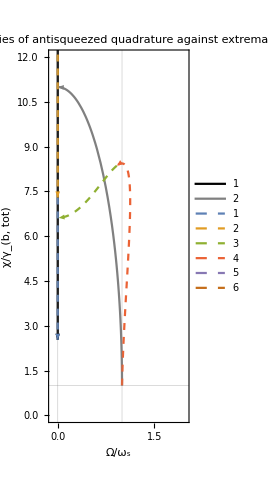

```mathematica
(*plot comparing antisqz-pole to sqz-minimum solutions*)
ϵ0=1. 10^-15;
plotRange0={{-0.1,2},{0,12}};
isArrowed0=True;
p1=plotPoleThreshold[0,plotRange0,{Black,Gray},False ,isArrowed0];
p2=plotSqzExtremePoints[ϵ0,ϵ0,plotRange0,Dashed,False,isArrowed0];
Show[p1,p2,PlotLabel->Style["degenerate internal squeezing\nparameters of LIGO Voyager\ncomparing singularities of antisqueezed quadrature\n against extrema (minima) of squeezed quadrature\nas a function of T_(l, a)∈(0,1) with T_(l, b)~0",10]]
```

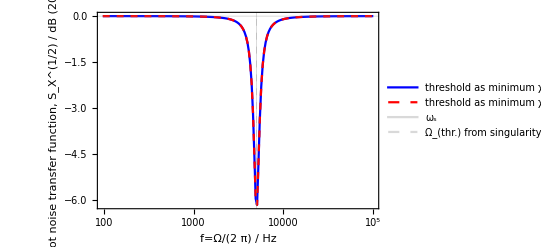

```mathematica
(*to-do: show different values of threshold in Sx (squeezed quadrature) plot
--> what does the pole definition correspond to? and why isn't it the minimum?*)
Clear[χPoleThresh,compareThresholdDefs]
χPoleThresh[γa0_,γbtot0_]:=If[γa0≠0,Min[(χ/.poleSol/.{γa->γa0,γbtot->γbtot0})],χ/.poleSol[[2]]/.{γa->γa0,γbtot->γbtot0}]
χSqzMinThresh[γa0_,γbtot0_,Rpd0_]:=Min[Select[χ/.minSol/.{γa->γa0,γbtot->γbtot0,Rpd->Rpd0},Not[#===Undefined]&]]

compareThresholdDefs[Tla0_,Tlb0_,Rpd0_]:=Block[{γa=γaFn[Tla0],γbtot=γbtotFn[Tlb0],Rpd=Rpd0},
LogLinearPlot[
{20 1/2 Log10[Sx1[2π f,χPoleThresh[γa,γbtot]]],
20 1/2 Log10[Sx1[2π f,χSqzMinThresh[γa,γbtot,Rpd]]]},{f,0,10^5},PlotRange->{All,0},Frame->True,FrameLabel->{{"shot noise transfer function,\nS_X^(1/2) / dB (20 log_10)",},{"f=Ω/(2  π) / Hz",StringForm["degenerate internal squeezing\nparameters of LIGO Voyager\nshot noise of squeezed quadrature at different threshold definitions\nT_(l, a)=``, T_(l, b)=``, R_PD=``",Tla0,Tlb0,Rpd0]}},GridLines->{{ωs/(2π),{Re[Ω/(2π)/.poleSol[[2]]],Dashed}},{0}},PlotLegends->LineLegend[{"threshold as minimum χ of\nsingularities of anti-sqz'd quadrature","threshold as minimum χ of\nminima of sqz'd quadrature"},LabelStyle->Directive[10]],PerformanceGoal->"Speed",PlotStyle->{Blue,{Red,Dashed},{Red,Dashed}}]]

ϵ0=1. 10^-10;
Legended[compareThresholdDefs[(*Tla*)0.05,ϵ0,ϵ0],LineLegend[{Directive[LightGray,Thick],Directive[LightGray,Dashed]},{"ω_s","Ω_(thr.) from singularity def"},LabelStyle->10,LegendLabel->"vertical gridlines"]]
```

Power::infy: Infinite expression 1/0. encountered.

value of anti-sqz.'d S_X at threshold values:  ∞

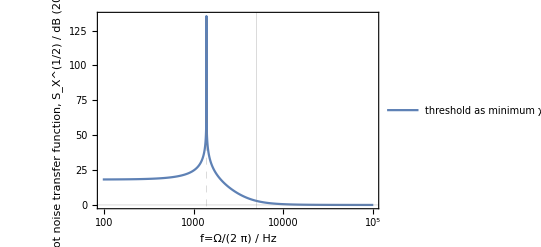

```mathematica
Block[{γa=γaFn[0.8],γbtot=γbtotFn[ϵ0],Rpd=ϵ0},
Print["value of anti-sqz.'d S_X at threshold values: "20 1/2 Log10[Sx1[Ω/.poleSol[[2]],-(γa+γbtot)]]];
LogLinearPlot[20 1/2 Log10[Sx1[2π f,-(γa+γbtot)]],{f,0,10^5},ClippingStyle->Red,Frame->True,FrameLabel->{{"shot noise transfer function,\nS_X^(1/2) / dB (20 log_10)",},{"f=Ω/(2  π) / Hz",StringForm["degenerate internal squeezing\nparameters of LIGO Voyager\nshot noise of anti-squeezed quadrature\nT_(l, a)=``, T_(l, b)=``, R_PD=``",0.7,0,0]}},GridLines->{{ωs/(2π),{Re[Ω/(2π)/.poleSol[[2]]],Dashed}},{0}},PlotLegends->LineLegend[{"threshold as minimum χ of\nsingularities of anti-sqz'd quadrature"},LabelStyle->Directive[10]],PerformanceGoal->"Quality",PlotPoints->10000,PlotRange->All]]
```

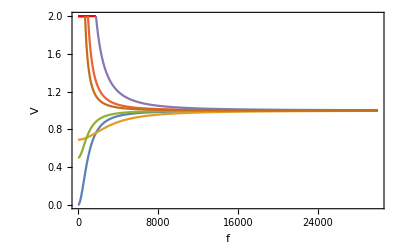

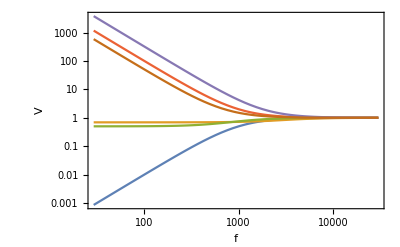

```mathematica
(*visualing robustness of anti-sqz pole to losses -- dOPO*)
dOPOFn[Ω_,χ_,Tlb_,Rpd_]:=1-(4 γR χ (1-Rpd))/((γbtotFn[Tlb]+χ)^2+Ω^2)
dOPOFnList={
Block[{Tlb0=0     },dOPOFn[2π f,γbtotFn[Tlb0],Tlb0,0]],
Block[{Tlb0=0.1},dOPOFn[2π f,γbtotFn[Tlb0],Tlb0,0]],
Block[{Tlb0=0},dOPOFn[2π f,γbtotFn[Tlb0],Tlb0,0.5]],
Block[{Tlb0=0     },dOPOFn[2π f,-γbtotFn[Tlb0],Tlb0,0]],
Block[{Tlb0=0.1},dOPOFn[2π f,-γbtotFn[Tlb0],Tlb0,0]],
Block[{Tlb0=0},dOPOFn[2π f,-γbtotFn[Tlb0],Tlb0,0.5]]};
Plot[dOPOFnList,{f,0,3 10^4},Frame->True,FrameLabel->{f,V},ClippingStyle->Red,PlotRange->{0,2}]
LogLogPlot[dOPOFnList,{f,0,3 10^4},Frame->True,FrameLabel->{f,V}]
```